## Import

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"negf.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

```mathematica
GetOrbitalΣ[Σd_]:=Module[{},
bands=(
{atomIndex,σ}=#;
Band[{orbInForAtomIn[[atomIndex]],orbInForAtomIn[[atomIndex]]}]->
σ*IdentityMatrix[MAXORB[types⟦atomIndex⟧]]
)&/@Σd;
SparseArray[bands,{norb,norb}]
]
```

## Ham gen

```mathematica
moleName="mcpp_60Au";
{atoms,types,bonds}=ImportXYZ[moleName<>".xyz"];
natom=Length[atoms]
```

178

```mathematica
h=DFTBSolver2[atoms,types];
s=DFTBSolver2[atoms,types,"S"];
```

```mathematica
(*self energy diagonal element: atom index, Im self energy[eV]*)
ΣdL=Table[{i,1},{i,102,122}];
ΣdR=Table[{i,1},{i,158,178}];
(*orbital-atom relation*)
orbInAtom=MAXORB/@types;
norb=Total[MAXORB/@types];
orbInForAtomIn=Accumulate[{1}~Join~orbInAtom][[1;;-2]];
(*self energy diagonal element applied to orbital: orbital index, Im self energy[Hartree]*)
ΣL=-I*GetOrbitalΣ[ΣdL];
ΣR=-I*GetOrbitalΣ[ΣdR];
```

## MOL

```mathematica
atomsListM=Append[Range[1,67],123];
atomsM=atoms⟦atomsListM⟧;
typesM=types⟦atomsListM⟧;
hM=DFTBSolver2[atomsM,typesM];
sM=DFTBSolver2[atomsM,typesM,"S"];
{eval,evec}=MyEigensystem[{hM,sM}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atomsM,typesM]
EF
```

{-4.33643,-4.2322,-4.28431,0.104235,107}

-4.28431

```mathematica
(*{eval,evec}=MyEigensystem[{h,s}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atoms,types]
EF*)
```

## Highlight Contact and Molecule

```mathematica
highlightAtom=Table[
{
If[MemberQ[ΣdL⟦All,1⟧,i],clr=Red,
If[MemberQ[ΣdR⟦All,1⟧,i],clr=Blue,
If[MemberQ[atomsListM,i],clr=Orange,
clr=Gray
];
];
];
clr,
Sphere[atoms⟦i⟧]},
{i,natom}
];
```

```mathematica
Graphics3D[
highlightAtom
]
```

-Graphics3D-

## NEGF run

```mathematica
{emin,emax,estep}={EF-2,EF+2,0.02};
```

```mathematica
et=Table[
{ϵ-EF,NEGFSystemWBΣS[ϵ,h,s,ΣL,ΣR]⟦1⟧},
{ϵ,emin,emax,estep}
]
```

{{-2.,0.993853},{-1.98,0.992543},{-1.96,0.993343},{-1.94,0.995524},{-1.92,0.99806},{-1.9,0.999875},{-1.88,1.00002},{-1.86,0.997784},{-1.84,0.992647},{-1.82,0.983791},{-1.8,0.969753},{-1.78,0.949631},{-1.76,0.924702},{-1.74,0.898791},{-1.72,0.877697},{-1.7,0.869781},{-1.68,0.95807},{-1.66,0.882306},{-1.64,0.908858},{-1.62,0.944396},{-1.6,0.978643},{-1.58,0.998747},{-1.56,0.992286},{-1.54,0.953402},{-1.52,0.886893},{-1.5,0.80578},{-1.48,0.724678},{-1.46,0.654099},{-1.44,0.599145},{-1.42,0.56112},{-1.4,0.53933},{-1.38,0.531738},{-1.36,0.533834},{-1.34,0.53496},{-1.32,0.512824},{-1.3,0.436779},{-1.28,0.305324},{-1.26,0.178071},{-1.24,0.0995538},{-1.22,0.0600686},{-1.2,0.0403687},{-1.18,0.0297385},{-1.16,0.0233937},{-1.14,0.0191831},{-1.12,0.0160867},{-1.1,0.0136772},{-1.08,0.0118604},{-1.06,0.0104699},{-1.04,0.00913284},{-1.02,0.00772071},{-1.,0.0063251},{-0.98,0.00504865},{-0.96,0.00395071},{-0.94,0.00305046},{-0.92,0.00233853},{-0.9,0.00178983},{-0.88,0.0013741},{-0.86,0.0010623},{-0.84,0.000829579},{-0.82,0.000656003},{-0.8,0.000526266},{-0.78,0.00042896},{-0.76,0.000355755},{-0.74,0.00030066},{-0.72,0.000259432},{-0.7,0.000229133},{-0.68,0.000207829},{-0.66,0.000194401},{-0.64,0.000188466},{-0.62,0.000190384},{-0.6,0.0002014},{-0.58,0.000223924},{-0.56,0.000262035},{-0.54,0.000322321},{-0.52,0.000415233},{-0.5,0.000557241},{-0.48,0.000774186},{-0.46,0.00110636},{-0.44,0.00161582},{-0.42,0.00239612},{-0.4,0.00358348},{-0.38,0.00536603},{-0.36,0.00798433},{-0.34,0.0117139},{-0.32,0.0168249},{-0.3,0.0235304},{-0.28,0.031955},{-0.26,0.0421634},{-0.24,0.0542607},{-0.22,0.0685317},{-0.2,0.0855714},{-0.18,0.10637},{-0.16,0.132334},{-0.14,0.165186},{-0.12,0.206615},{-0.1,0.257462},{-0.08,0.316304},{-0.06,0.377915},{-0.04,0.433022},{-0.02,0.470664},{0.,0.482306},{0.02,0.465121},{0.04,0.423063},{0.06,0.365574},{0.08,0.303912},{0.1,0.246933},{0.12,0.199094},{0.14,0.16114},{0.16,0.131816},{0.18,0.109228},{0.2,0.0915512},{0.22,0.0772857},{0.24,0.0653112},{0.26,0.0548717},{0.28,0.0455391},{0.3,0.0371548},{0.32,0.0297359},{0.34,0.0233621},{0.36,0.0180797},{0.38,0.013854},{0.4,0.0105737},{0.42,0.00808371},{0.44,0.00622076},{0.46,0.00483706},{0.48,0.00381101},{0.5,0.00304833},{0.52,0.00247854},{0.54,0.0020501},{0.56,0.00172571},{0.58,0.00147853},{0.6,0.00128923},{0.62,0.00114387},{0.64,0.00103239},{0.66,0.000947511},{0.68,0.000883961},{0.7,0.000837975},{0.72,0.000806911},{0.74,0.000788999},{0.76,0.000783181},{0.78,0.000789009},{0.8,0.000806606},{0.82,0.000836673},{0.84,0.000880548},{0.86,0.000940337},{0.88,0.00101912},{0.9,0.0011213},{0.92,0.00125312},{0.94,0.00142358},{0.96,0.00164585},{0.98,0.00193987},{1.,0.00233719},{1.02,0.00289067},{1.04,0.00369646},{1.06,0.00495004},{1.08,0.00711718},{1.1,0.0116033},{1.12,0.0246674},{1.14,0.109818},{1.16,0.578162},{1.18,0.0653145},{1.2,0.0376069},{1.22,0.0376329},{1.24,0.0477829},{1.26,0.0689416},{1.28,0.109002},{1.3,0.187281},{1.32,0.347211},{1.34,0.653282},{1.36,0.979017},{1.38,0.891335},{1.4,0.60563},{1.42,0.404258},{1.44,0.286453},{1.46,0.215859},{1.48,0.170997},{1.5,0.140851},{1.52,0.119635},{1.54,0.104138},{1.56,0.0924685},{1.58,0.083447},{1.6,0.0762965},{1.62,0.0704824},{1.64,0.0656287},{1.66,0.0614767},{1.68,0.0578671},{1.7,0.0547342},{1.72,0.0521056},{1.74,0.0501061},{1.76,0.048975},{1.78,0.0491169},{1.8,0.0512327},{1.82,0.0566488},{1.84,0.0681736},{1.86,0.092559},{1.88,0.148503},{1.9,0.293964},{1.92,0.662003},{1.94,1.00689},{1.96,0.998013},{1.98,0.782622},{2.,0.114644}}

```mathematica
Export["trans.m",et];
```

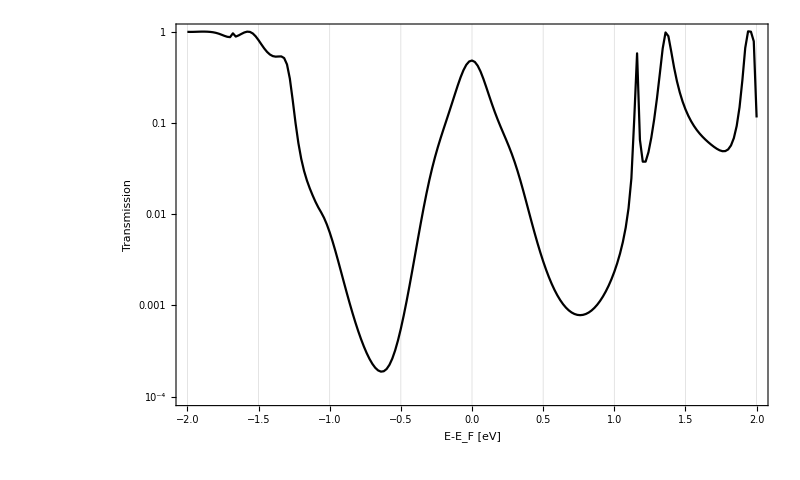

```mathematica
ListLogPlot[{et},GridLines->{eval-EF,None},
FrameLabel->{"E-E_F [eV]"," Transmission "},
Frame->True,
AspectRatio->0.6,
(*PlotLegends->Placed[{"BZ","CJ"},{0.55,0.8}],*)
Joined->True,
PlotStyle->{Black,Thick},
ImageSize->{800,500},
Axes->False,
styles]
```